# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out Omicron sub-lineages BA.1 / 21K, BA.2 / 21L, BA.4 / 22A, BA.5 / 22B, BA.2.12.1 / 22C

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries-split

```mathematica
dataset="omicron-countries-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L","Omicron 22A","Omicron 22B","Omicron 22C"};
```

```mathematica
variantLabels={"other","Delta","Omicron BA.1","Omicron BA.2","Omicron BA.4","Omicron BA.5","Omicron BA.2.12.1"};
```

```mathematica
n=Length[variants]
```

7

### Colors

```mathematica
start[n_]:=0.1;
```

```mathematica
stop[n_]:=0.98;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Join[{Gray,RGBColor[{0.572,0.384,0.141}]},makeColors[n-2]]
```

{GrayLevel[0.5],RGBColor[{0.572, 0.384, 0.141}],RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.31246632, 0.59399708, 0.72838912],RGBColor[0.5737267600000001, 0.73875072, 0.38814183999999996],RGBColor[0.86951232, 0.6566998, 0.23336048],RGBColor[0.86399836, 0.18297864000000005, 0.14120096000000001]}

```mathematica
legendPanel=PointLegend[colors[[2;;n]],variantLabels[[2;;n]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Austria","Portugal"};
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-02-13

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-07-01

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-07-01

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{Australia,Austria,Belgium,Brazil,Canada,Denmark,France,Germany,India,Indonesia,Ireland,Israel,Italy,Japan,Mexico,Netherlands,New Zealand,Peru,Portugal,Singapore,South Korea,Spain,Sweden,Switzerland,United Kingdom,USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{Australia,Belgium,Brazil,Canada,Denmark,France,Germany,India,Indonesia,Ireland,Israel,Italy,Japan,Mexico,Netherlands,New Zealand,Peru,Singapore,South Korea,Spain,Sweden,Switzerland,United Kingdom,USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,2.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{variantsWithValues,medians,finalDates,finalValues},
variantsWithValues=Flatten[Map[If[Length[rtGather[country,#]]>0,#,{}]&,variants]];
medians=Map[Last[rtGather[country,#]]&,variantsWithValues];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,2.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;n]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

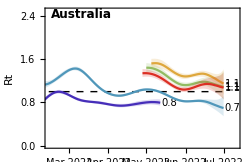
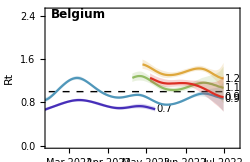
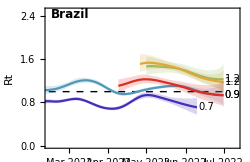
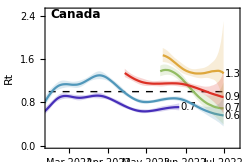
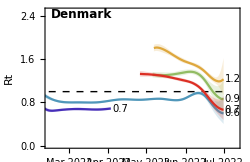
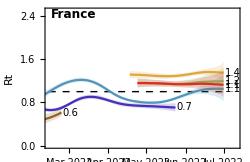
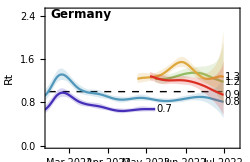
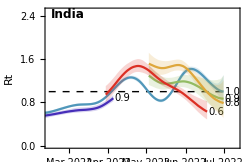
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],rtPanels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-rt.png

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,r_upper_95→5,r_lower_95→6,r_upper_80→7,r_lower_80→8,r_upper_50→9,r_lower_50→10,median_freq→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[11]]>0.005];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{variantsWithValues,medians,finalDates,finalValues},
variantsWithValues=Flatten[Map[If[Length[rtGather[country,#]]>0,#,{}]&,variants]];
medians=Map[Last[rGather[country,#]]&,variantsWithValues];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,16]},
{-0.35,0.4}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;n]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,n}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

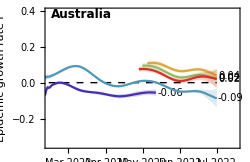
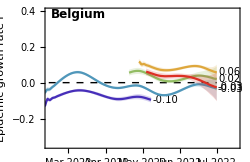
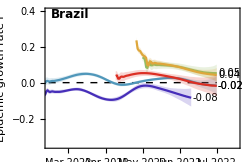
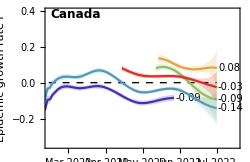
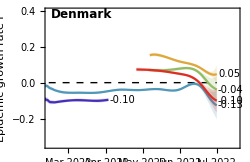
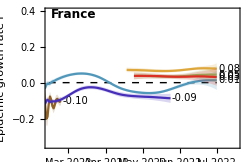
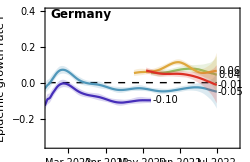
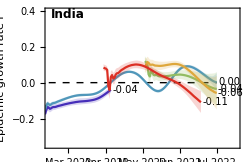
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-little-r.png

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{62,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{50,1020000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,n}]]
```

```mathematica
casesPanels=Map[countryPrevalencePlot,countries];
```

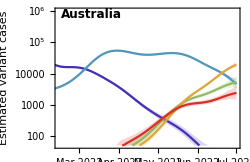
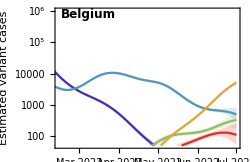
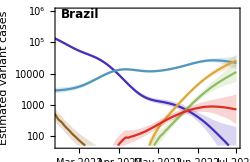
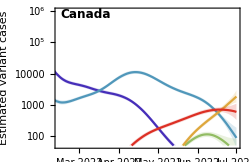
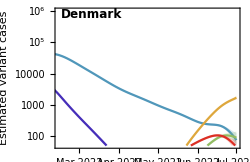
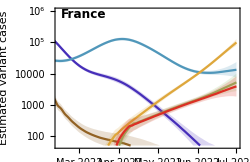
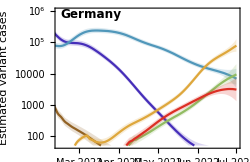
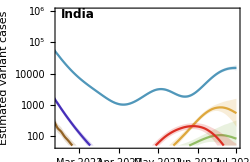
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],casesPanels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,n}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

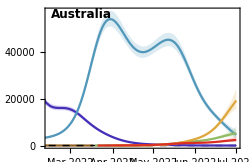
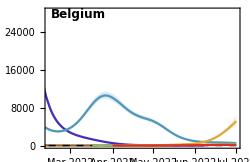
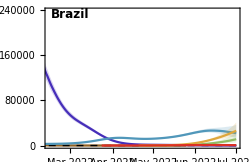
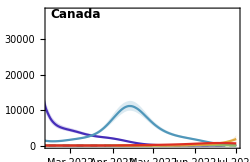
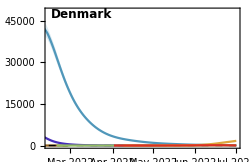
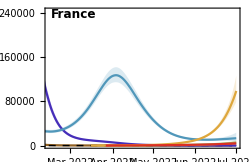
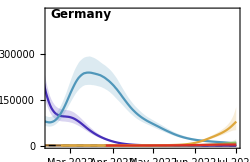
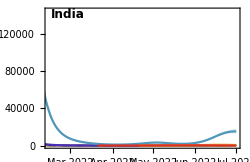
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-cases.png

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,2,n}]]
```

```mathematica
panels=Map[countryFrequencyPlot,countries];
```

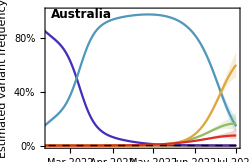
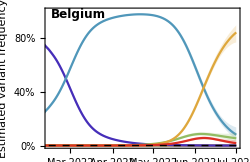
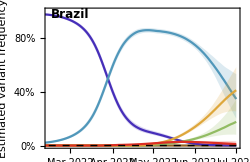
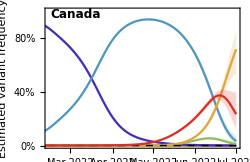
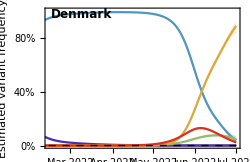
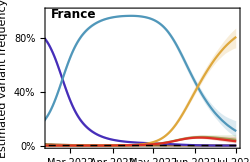
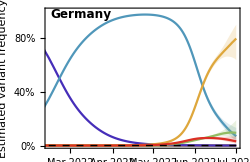
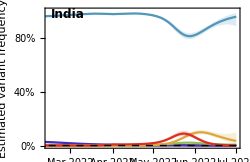
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-estimated-frequency.png

## Composite

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],Join[casesPanels,rtPanels]],gridCount],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Export["figures/" <> dataset <> "_rt-cases.png", fig, "PNG", ImageResolution -> 300]

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{trajectories,pos,lines,points},
trajectories=Map[phaseGather[country,#]&,variants];
pos=Flatten[Position[Map[Length,trajectories],x_/;x>0]];
trajectories=trajectories[[pos]];
lines=ListLogLinearPlot[trajectories,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},Joined->True,PlotMarkers->None,PlotStyle->colors[[pos]],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}];
points=ListLogLinearPlot[Map[{Last[#]}&,trajectories],Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},PlotRange->{{2,700},
{-0.25,0.4}},Joined->False,PlotMarkers->{"•",Scaled[0.12]},PlotStyle->colors[[pos]],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}];
Show[lines,points]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_variant-cases-vs-rt.png

## BA.1/BA.2 incidence vs BA.4/BA.5 growth rates

There is a hypothesis circulating that countries with larger BA.2 waves should be spared from BA.4/BA.5 waves compared to countries with larger BA.1 waves

```mathematica
perCapitaTotalPGather[country_,variant_]:=Module[{popSize,totalCases},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
totalCases=Total[pGather[country,variant][[All,2]]];
totalCases/popSize
]
```

```mathematica
perCapitaTotalPGather["USA","Omicron 21K"]
```

0.0139287

```mathematica
totalCasesOmicronBA1=Map[perCapitaTotalPGather[#,"Omicron 21K"]&,countries]
```

{0.0328371,0.0254911,0.0186647,0.0105084,0.00984508,0.0386855,0.0717328,0.0000241037,0.00321854,0.0144292,0.0616178,0.0334683,0.0248001,0.00524973,0.0859888,0.0354517,0.00821461,0.0323812,0.0873133,0.018936,0.00708572,0.0574978,0.0233216,0.0139287}

```mathematica
totalCasesOmicronBA2=Map[perCapitaTotalPGather[#,"Omicron 21L"]+perCapitaTotalPGather[#,"Omicron 22C"]&,countries]
```

{0.166632,0.0576032,0.00952586,0.0155104,0.21808,0.109857,0.178108,0.00117462,0.00292333,0.0625876,0.075188,0.0729239,0.0248246,0.00154336,0.118141,0.230385,0.00182484,0.133728,0.249891,0.0311431,0.0214543,0.102629,0.0620788,0.0189958}

```mathematica
Correlation[totalCasesOmicronBA1,totalCasesOmicronBA2]
```

0.630074

```mathematica
fig=ListPlot[Transpose[{totalCasesOmicronBA1,totalCasesOmicronBA2}],Frame->{True,True,False,False},FrameLabel->{"Total BA.1 cases per capita","Total BA.2 cases per capita"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,PlotMarkers->{"•",Scaled[0.12]},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},
Epilog->{Text[Style["r = "<>ToString[Round[Correlation[totalCasesOmicronBA1,totalCasesOmicronBA2],0.01]],Black,FontSize->12,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,-1}]},ImagePadding->{{45,10},{35,15}},PlotRangeClipping->False]
```

-Graphics-

```mathematica
fractionCasesBA1=totalCasesOmicronBA1/(totalCasesOmicronBA1+totalCasesOmicronBA2)
```

{0.164623,0.306773,0.66209,0.403878,0.0431944,0.260433,0.287114,0.0201077,0.524033,0.187352,0.450403,0.314575,0.499754,0.772804,0.421246,0.133359,0.818233,0.194939,0.258933,0.378121,0.248273,0.359077,0.273085,0.423049}

```mathematica
latestGrowthRate[country_,variant_]:=Module[{series},
series=rtGather[country,variant];
If[Length[series]>0,series[[-1,2]],Null]
]
```

```mathematica
latestGrowthRate["Canada","Omicron 22A"]
```

0.687684

```mathematica
averageGrowthRateOmicronBA4BA5=Map[Mean[DeleteCases[{latestGrowthRate[#,"Omicron 22A"],latestGrowthRate[#,"Omicron 22B"]},Null]]&,countries]
```

{1.11957,1.15626,1.20124,1.01212,1.04468,1.2744,1.22868,0.826026,1.06258,0.875407,0.950836,1.25474,1.36463,1.33586,1.05275,1.27744,1.21732,1.24287,1.18826,1.15521,0.893237,1.04693,1.08869,1.37776}

```mathematica
fig=ListPlot[Transpose[{fractionCasesBA1,averageGrowthRateOmicronBA4BA5}],Frame->{True,True,False,False},FrameLabel->{"Fraction BA.1 of BA.1+BA.2 cases","Average current Rt of BA.4 and BA.5"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,PlotMarkers->{"•",Scaled[0.12]},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.1}],Automatic}},
Epilog->{Text[Style["r = "<>ToString[Round[Correlation[fractionCasesBA1,averageGrowthRateOmicronBA4BA5],0.01]],Black,FontSize->12,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,-1}]},ImagePadding->{{45,10},{35,15}},PlotRangeClipping->False]
```

-Graphics-